# lorentzian smearing

## δ switch, l smear, go futher with the transition probability

## the smearing function

```mathematica
f[x_]:=σ/π 1/(x^2+σ^2)
ftil[k_]:=FourierTransform[f[x],x,k,FourierParameters->{1,-1},Assumptions->σ∈Reals&&σ>0]
```

#### simplify the fourier transform

```mathematica
ftil[k]
```

ⅇ^(-k σ) (ⅇ^(2 k σ) HeavisideTheta[-k]+HeavisideTheta[k])

```mathematica
Simplify[%,Assumptions->σ∈Reals&&σ>0]
```

```mathematica
ftilGs[k_]:=ⅇ^(-1/4 k^2 σ^2)
```

## the transition probability

```mathematica
ggintegrand[k_]:=(1-2*α)/(2π)*ⅇ^(-ε*k)*k*ftil[k]^2
```

#### with an ε regularized cutoff (exp)

```mathematica
Integrate[ggintegrand[k],{k,0,∞}]
```

ConditionalExpression[(1-2 α)/(2 π (ε+2 σ)^2),Re[ε+2 σ]>0]

```mathematica
Simplify[%,Assumptions->σ∈Reals&&σ>0&&ε∈Reals&&ε>0&&Ω∈Reals]
```

```mathematica
pertexp[σ_]:=(1-2 α)/(2 π (ε+2 σ)^2)
```

```mathematica
pexp[σ_]:=α+λ^2*pertexp[σ]
```

#### with no cutoff (ε:=0)

```mathematica
Simplify[pertexp[σ],Assumptions->ε==0]
```

```mathematica
pertnone[σ_]:=(1-2 α)/(8 π σ^2)
```

```mathematica
pnone[σ_]:=α+λ^2*pertnone[σ]
```

#### with a sharp cutoff (ε:=0 and integrate only up to a constant)

```mathematica
Integrate[ggintegrand[k],{k,0,5*Ω}]
```

ConditionalExpression[-1/(2 π)(-1+2 α) ((ⅇ^(-5 (ε-2 σ) Ω) (-1+ⅇ^(5 (ε-2 σ) Ω)-5 ε Ω+10 σ Ω) HeavisideTheta[-Ω])/(ε-2 σ)^2+(ⅇ^(-5 (ε+2 σ) Ω) (-1+ⅇ^(5 (ε+2 σ) Ω)-5 (ε+2 σ) Ω) HeavisideTheta[Ω])/(ε+2 σ)^2),Ω∈Reals]

```mathematica
Simplify[Out[25],Assumptions->σ∈Reals&&σ>0&&η∈Reals&&η>0&&ε==0&&Ω∈Reals&&Ω>0]
```

```mathematica
pertsharp[σ_]:=-((-1+2 α) (1-ⅇ^(-10 σ Ω) (1+10 σ Ω)))/(8 π σ^2)
```

```mathematica
psharp[σ_]:=α+λ^2*pertsharp[σ]
```

#### with a different cutoff (later) (ε:=0 and cutoff[k_]:=something)

## plot p v σ

#### assign the parameters numbers

```mathematica
Ω:=1
α:=0
λ:=0.1
ε:=.25
```

#### clear the parameters of their numbers when necessary

```mathematica
Clear[Ω];Clear[α];Clear[λ];Clear[ε];
```

#### plot p v σ

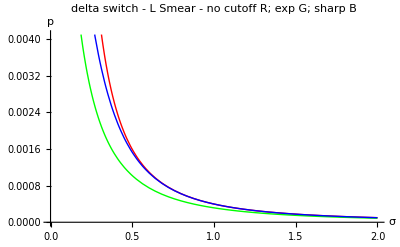

```mathematica
Plot[{pnone[σ],pexp[σ],psharp[σ]},{σ,0.1,2},
AxesLabel->{σ,p},
PlotRange->Automatic,
PlotStyle->{Red,Green,Blue},
PlotLabel->Style["delta switch - L Smear -\n no cutoff R; exp G; sharp B",FontSize->16]]
```

## status

i think we had expected that p would diverge for δ - δ. if that is the case it makes sense for p to diverge in the σ→0 limit for no cutoff. also indicates that a sharp cutoff has a larger effect on the effective size in the δ switching case than in the G switching case.